```mathematica
DD = 0;
r = 1;
ro1 =1.0;
p1 = 1.0;
u1 = 1.0;
g = 5/3;
B1 = 0;
s = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 == ro*u*(u - DD)+ p&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals]
M1 = (u1-DD)/Sqrt[g*p1/ro1]
s2 = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 + (B1^2)/2== ro*u*(u - DD)+ p+ (B^2)/2&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2+ B1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2+ B^2/2) + p * u ,{ro, u, p,B},Reals];
M1 = (u1-DD)/Sqrt[g*p1/ro1];
M0 = (u1-DD)/Sqrt[g*0.0015/0.25];
T1=p1/ro1;
```

{{ro→0.666667,u→1.5,p→0.5},{ro→1.,u→1.,p→1.}}

0.774597

NSolve::svars: Equations may not give solutions for all "solve" variables.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{p,ro,u}/.{{ro->0.6666666666666666,u->1.5,p->0.5},{ro->0.9999999999999998,u->1.0000000000000002,p->0.9999999999999998}}
```

{{0.5,0.666667,1.5},{1.,1.,1.}}

```mathematica
n1 = 0.58;
n2=0.128;
mp=1.672*10^(-24);
ro1=n1*mp;
ro2=n2*mp;
v1=412*10^5;
v2=439*10^5;
p1=4.1*10^(-12);
p2=185*10^(-15);
g=5/3;
D1=(n1*v1-n2*v2)/(n1-n2) /10^5
D2=(p2-p1+ro2* v2^2-ro1* v1^2)/(ro2 *v2-ro1* v1) /10^5
D3=(2 g p1 v1-ro1 v1^3+g ro1 v1^3-2 g p2 v2+ro2 v2^3-g ro2 v2^3)/(2 p1-2 p2-ro1 v1^2+g ro1 v1^2+ro2 v2^2-g ro2 v2^2) /10^5
```

404.354

404.98

405.628

```mathematica
Solve[ro1*(v1 - DD)*(p1/(ro1*(g-1)) + v1^2/2) + p1 * v1==ro2*(v2 - DD)*(p2/(ro2*(g-1)) + (v2^2)/2) + p2 * v2,DD]
```

{{DD→(2 g p1 v1-ro1 v1^3+g ro1 v1^3-2 g p2 v2+ro2 v2^3-g ro2 v2^3)/(2 p1-2 p2-ro1 v1^2+g ro1 v1^2+ro2 v2^2-g ro2 v2^2)}}

```mathematica
10^-3//N
```

0.001

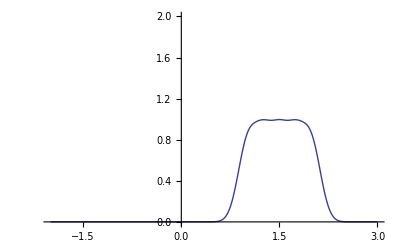

```mathematica
Plot[0.7*(Exp[-((x-1)/0.2)^2] + Exp[-((x-1.25)/0.2)^2]+ Exp[-((x-2)/0.2)^2]+ Exp[-((x-1.5)/0.2)^2]+ Exp[-((x-1.75)/0.2)^2]),{x,-2,3}, PlotRange->{0,2}]
```

```mathematica
4*π*Integrate[x^2 *0.7*Exp[-((x-1)/0.2)^2]/(Sqrt[π*0.2]^3),{x,-5,5}]
4*π*Integrate[x^2 *x*0.7*Exp[-((x-1)/0.2)^2]/(Sqrt[π*0.2]^3),{x,-5,5}]
4*π*Integrate[x^2 *x^2 * 0.7*Exp[-((x-1)/0.2)^2]/(Sqrt[π*0.2]^3),{x,-5,5}]
```

6.38621

6.63665

7.01982

```mathematica
Integrate[v*Exp[-u^2 / cp^2 - v^2 / cp^2],{u,-∞,∞},{v,0,∞},{θ,0,2π},GenerateConditions->False]
```

√(1/cp^2) cp^4 π^(3/2)

```mathematica
Integrate[v*Exp[-u^2 / cp^2 - v^2 / cp^2]/(cp^3 π^(3/2)),{v,0,∞},{θ,0,2π},GenerateConditions->False]
```

(ⅇ^(-u^2/cp^2))/(cp √π)